```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/量子化学实验报告/figures"];
```

```mathematica
list1={{418.131,"HF 6-31G"},{420.686,"B3LYP 6-31G（DFT）"},{9.48884*10^-2,"PM6 (Semi-empirical)"}}
```

{{418.131,HF 6-31G},{420.686,B3LYP 6-31G（DFT）},{0.0948884,PM6 (Semi-empirical)}}

```mathematica
"Methods.eps"~Export~BarChart[#1,ChartLabels->Placed[#2,Top],ImageSize->Large,Axes->False,Frame->True,AxesLabel->{"Type","Energy/Hartree"}]&@@Transpose[list1]
```

Methods.eps

```mathematica
list2=Transpose@{{{418.131,420.686},"6-31G"},{{415.961,418.501},"3-21G"},{{418.340,420.855},"cc-pVDZ"},{{418.186,420.763},"LanL2DZ"}}
```

{{{418.131,420.686},{415.961,418.501},{418.34,420.855},{418.186,420.763}},{6-31G,3-21G,cc-pVDZ,LanL2DZ}}

```mathematica
"Sets.eps"~Export~BarChart[#1,ChartLabels->Placed[#2,Top],ChartLegends->{"HF","DFT"},ImageSize->Large,Axes->False,Frame->True,FrameLabel->{"Type","Energy/Hartree"},PlotRange->{Automatic,{0,420}}]&@@list2
```

Sets.eps

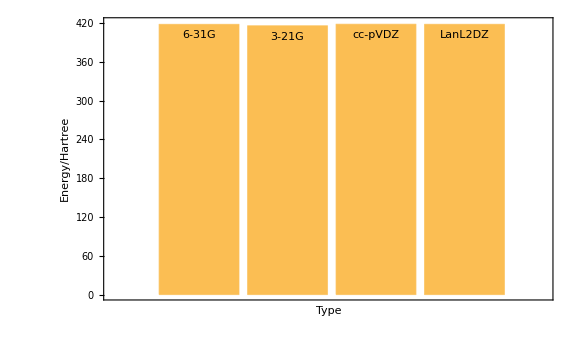

```mathematica
BarChart[#1,ChartLabels->Placed[#2,Top],ImageSize->Large,Axes->False,Frame->True,FrameLabel->{Style["Type",20],Style["Energy/Hartree",20]},PlotRange->{Automatic,{0,420}}]&@@list2
```

```mathematica
"benzoicmethanolIR.eps"~Export~ListLinePlot[{{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/benzoicmethanolhf_ir.txt","Table"],{_Real,_Real,_Real}],{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/2nd-pack/benzoicmethanoldft_ir.txt","Table"],{_Real,_Real,_Real}]},PlotRange->All,Frame->True,PlotStyle->{{Black,Thickness[0.002],Dashed},{Black,Thickness[0.002]}},PlotLegends->{"HF","DFT"},ImageSize->Large]
```

benzoicmethanolIR.eps

```mathematica
"benzoicformateIR.eps"~Export~ListLinePlot[{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/benzoic_formate_ir.txt","Table"],{_Real,_Real,_Real}],PlotRange->All,Frame->True,PlotStyle->{Black,Thickness[0.003]},ImageSize->Large,Axes->False]
```

benzoicformateIR.eps

```mathematica
figure=-Graphics-
```

-Graphics-

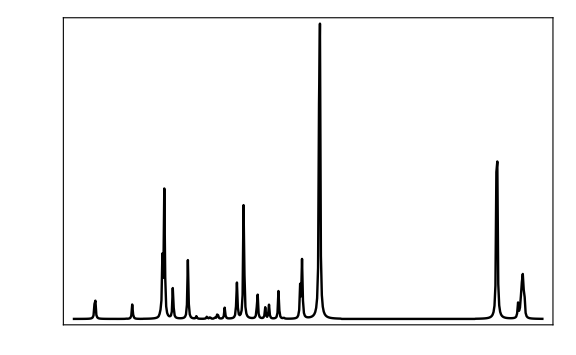

```mathematica
graph=ListLinePlot[{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/benzoic_formate_ir.txt","Table"],{_Real,_Real,_Real}],PlotRange->All,Frame->True,PlotStyle->{Black,Thickness[0.003]},ImageSize->Large,Axes->False,FrameTicks->False]~Rotate~Pi
```

```mathematica
"benzoicformateIR.eps"~Export~(graph=ListLinePlot[{{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/benzoic_formate_ir.txt","Table"],{_Real,_Real,_Real}],{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/2nd-pack/benzoic_formatedft_ir.txt","Table"],{_Real,_Real,_Real}]},PlotRange->All,Frame->True,PlotStyle->{{Black,Thickness[0.002],Dashed},{Black,Thickness[0.002]}},PlotLegends->{"HF","DFT"},ImageSize->Large,Axes->False])
```

benzoicformateIR.eps

```mathematica
TableForm[{#2,#1}&@@Transpose[list1]]//TeXForm
```

\begin{array}{ccc}
 \text{HF 6-31G} & \text{B3LYP 6-31G$\unicode{ff08}$DFT$\unicode{ff09}$} & \text{PM6
   (Semi-empirical)} \\
 418.131 & 420.686 & 0.0948884 \\
\end{array}

```mathematica
TableForm[{#2,#1}&@@list2]//TeXForm
```

\begin{array}{cccc}
 \text{6-31G} & \text{3-21G} & \text{cc-pVDZ} & \text{LanL2DZ} \\
 418.131 & 415.961 & 418.34 & 418.186 \\
\end{array}

```mathematica
RunProcess[{"ssh","user@server"},ProcessEnvironment-><|"PATH"->"/usr/local/bin:/usr/bin:/bin:/usr/sbin:/sbin:/opt/X11/bin:/Library/TeX/texbin"|>]
```

<|ExitCode→255,StandardOutput→,StandardError→Pseudo-terminal will not be allocated because stdin is not a terminal.\r
ssh: Could not resolve hostname server: nodename nor servname provided, or not known\r
|>

```mathematica
ListLinePlot[{#1,#2}&@@@Cases[Import["/Volumes/WALTER FENG/Gaussian/benzoic_formate_ir.txt","Table"],{_Real,_Real,_Real}],PlotRange->All,Frame->True,PlotStyle->{Black,Thickness[0.003]},ImageSize->Large,Axes->False]
```

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/Gaussian/3rd-pack"];
```

```mathematica
FileNames["*_uvvis.TXT"]
```

{acetylannilinepossiblebyproduct2_uvvis.txt,aspirinexcitedoptfreq2ndtry_uvvis.txt,aspirinexcitedoptfreqhf_uvvis.txt,aspirinexcitedoptfreq_uvvis.txt,sorbictddft_uvvis.txt,sorbictdft2ndtry_uvvis.txt,sorbictdftbvp86_uvvis.txt}

```mathematica
"aspirinuvvis.eps"~Export~ListLinePlot[{#1,#2}&@@@Cases[Import[#,"Table"],{_Real,_Real,_Real}]&/@{"aspirinexcitedoptfreq_uvvis.txt","aspirinexcitedoptfreq2ndtry_uvvis.txt","aspirinexcitedoptfreqhf_uvvis.txt"},PlotRange->{{0,800},All},Frame->True,PlotStyle->{{Black,Dashed},{Black,DotDashed},Black},ImageSize->Large,Axes->False,PlotLegends->{{"B3LYP","B3LYP2ndtry","HF"}}]
```

aspirinuvvis.eps

```mathematica
"sorbicaciduvvis.eps"~Export~ListLinePlot[{#1,#2}&@@@Cases[Import[#,"Table"],{_Real,_Real,_Real}]&/@{"sorbictddft_uvvis.txt","sorbictdft2ndtry_uvvis.txt","sorbictdftbvp86_uvvis.txt"},PlotRange->{{0,700},All},Frame->True,PlotStyle->{{Black,Dashed},{Black,DotDashed},{Black}},ImageSize->Large,Axes->False,PlotLegends->{"B3LYP","HF","BVP86"}]
```

sorbicaciduvvis.eps

```mathematica
string1=ImportString["      1          6           0       -0.078414    0.343956   -0.109123
      2          6           0        1.318500   -0.101445   -0.025263
      3          6           0        2.332288    0.847131   -0.042461
      4          6           0        2.053282    2.231249   -0.141465
      5          6           0        0.720839    2.692264   -0.206551
      6          6           0       -0.317280    1.784114   -0.182309
      7          1           0        3.358841    0.509928    0.016451
      8          1           0        2.875308    2.938109   -0.164118
      9          1           0        0.518615    3.756549   -0.262360
     10          1           0       -1.346047    2.117180   -0.198059
     11          6           0        1.670057   -1.529596    0.048008
     12          8           0        0.969086   -2.506812   -0.233899
     13          8           0        2.988619   -1.710971    0.481414
     14          1           0        3.178376   -2.672934    0.491281
     15          8           0       -1.054917   -0.453994   -0.107985
     16          6           0       -3.202669    0.084337    0.076839
     17          8           0       -3.400599    0.456399    1.213446
     18          6           0       -3.485682   -1.126976   -0.736700
     19          1           0       -3.016747   -2.000134   -0.267130
     20          1           0       -4.572635   -1.254721   -0.780533
     21          1           0       -3.078748   -1.021163   -1.745194","Table"]
```

{{1,6,0,-0.078414,0.343956,-0.109123},{2,6,0,1.3185,-0.101445,-0.025263},{3,6,0,2.33229,0.847131,-0.042461},{4,6,0,2.05328,2.23125,-0.141465},{5,6,0,0.720839,2.69226,-0.206551},{6,6,0,-0.31728,1.78411,-0.182309},{7,1,0,3.35884,0.509928,0.016451},{8,1,0,2.87531,2.93811,-0.164118},{9,1,0,0.518615,3.75655,-0.26236},{10,1,0,-1.34605,2.11718,-0.198059},{11,6,0,1.67006,-1.5296,0.048008},{12,8,0,0.969086,-2.50681,-0.233899},{13,8,0,2.98862,-1.71097,0.481414},{14,1,0,3.17838,-2.67293,0.491281},{15,8,0,-1.05492,-0.453994,-0.107985},{16,6,0,-3.20267,0.084337,0.076839},{17,8,0,-3.4006,0.456399,1.21345},{18,6,0,-3.48568,-1.12698,-0.7367},{19,1,0,-3.01675,-2.00013,-0.26713},{20,1,0,-4.57264,-1.25472,-0.780533},{21,1,0,-3.07875,-1.02116,-1.74519}}

```mathematica
string2="      1          6           0       -0.024638    0.391388   -0.162740
      2          6           0        1.333614   -0.132951   -0.004963
      3          6           0        2.401847    0.759763    0.062832
      4          6           0        2.213232    2.151824   -0.035773
      5          6           0        0.921383    2.683898   -0.224615
      6          6           0       -0.165907    1.836848   -0.297330
      7          1           0        3.401430    0.361608    0.182346
      8          1           0        3.071048    2.812995    0.029887
      9          1           0        0.787339    3.757822   -0.309460
     10          1           0       -1.168067    2.222806   -0.435565
     11          6           0        1.597670   -1.578890    0.040276
     12          8           0        0.835662   -2.511361   -0.242550
     13          8           0        2.910533   -1.852574    0.441515
     14          1           0        3.035750   -2.823280    0.427416
     15          8           0       -1.061793   -0.363485   -0.156892
     16          6           0       -3.296552    0.120339    0.041885
     17          8           0       -3.528177    0.779670    0.999714
     18          6           0       -3.562797   -1.236015   -0.485588
     19          1           0       -3.411356   -1.988837    0.299740
     20          1           0       -4.601112   -1.282082   -0.833967
     21          1           0       -2.871946   -1.456255   -1.298607"~ImportString~"Table"
```

{{1,6,0,-0.024638,0.391388,-0.16274},{2,6,0,1.33361,-0.132951,-0.004963},{3,6,0,2.40185,0.759763,0.062832},{4,6,0,2.21323,2.15182,-0.035773},{5,6,0,0.921383,2.6839,-0.224615},{6,6,0,-0.165907,1.83685,-0.29733},{7,1,0,3.40143,0.361608,0.182346},{8,1,0,3.07105,2.813,0.029887},{9,1,0,0.787339,3.75782,-0.30946},{10,1,0,-1.16807,2.22281,-0.435565},{11,6,0,1.59767,-1.57889,0.040276},{12,8,0,0.835662,-2.51136,-0.24255},{13,8,0,2.91053,-1.85257,0.441515},{14,1,0,3.03575,-2.82328,0.427416},{15,8,0,-1.06179,-0.363485,-0.156892},{16,6,0,-3.29655,0.120339,0.041885},{17,8,0,-3.52818,0.77967,0.999714},{18,6,0,-3.5628,-1.23602,-0.485588},{19,1,0,-3.41136,-1.98884,0.29974},{20,1,0,-4.60111,-1.28208,-0.833967},{21,1,0,-2.87195,-1.45626,-1.29861}}

```mathematica
Thread[Join[string1//Transpose,string2//Drop[#,3]&/@#&//Transpose]]//TableForm//TeXForm
```

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[string1,string2].

\text{Transpose}[\text{string1},\text{string2}]

```mathematica
string3="      1          6           0        4.087218   -0.110023    0.000045
      2          1           0        4.835950    0.687375   -0.000531
      3          1           0        4.279088   -0.740047    0.881397
      4          1           0        4.278786   -0.741061   -0.880641
      5          6           0        2.694593    0.444497   -0.000039
      6          1           0        2.584885    1.528432   -0.000138
      7          6           0        0.242482    0.177252   -0.000019
      8          6           0       -0.913503   -0.639190   -0.000101
      9          1           0        0.111445    1.257226   -0.000001
     10          1           0       -0.809813   -1.717938   -0.000114
     11          6           0       -2.183076   -0.144340   -0.000136
     12          8           0       -3.355089   -0.798627    0.000100
     13          8           0       -2.451116    1.214159    0.000035
     14          1           0       -3.411195    1.410942    0.000162
     15          6           0        1.556949   -0.327512    0.000028
     16          1           0        1.672513   -1.413297    0.000121"~ImportString~"Table";
string4="      1          6           0        4.069054   -0.104990   -0.000012
      2          1           0        4.789427    0.702954   -0.003637
      3          1           0        4.266996   -0.713807    0.876720
      4          1           0        4.264870   -0.719837   -0.872988
      5          6           0        2.658374    0.426498   -0.000113
      6          1           0        2.545775    1.497392   -0.000252
      7          6           0        0.204815    0.189249    0.000064
      8          6           0       -0.881179   -0.604074    0.000056
      9          1           0        0.080340    1.255328    0.000126
     10          1           0       -0.773010   -1.671965    0.000010
     11          6           0       -2.219061   -0.124722    0.000193
     12          8           0       -3.265674   -0.893620   -0.000163
     13          8           0       -2.462330    1.250899   -0.000026
     14          1           0       -3.384337    1.490618    0.000048
     15          6           0        1.562750   -0.330989    0.000040
     16          1           0        1.665455   -1.404751    0.000111"~ImportString~"Table";
Thread[Join[string3//Transpose,string4//Drop[#,3]&/@#&//Transpose]]//TableForm//TeXForm
```

\begin{array}{ccccccccc}
 1 & 6 & 0 & 4.08722 & -0.110023 & 0.000045 & 4.06905 & -0.10499 & -0.000012 \\
 2 & 1 & 0 & 4.83595 & 0.687375 & -0.000531 & 4.78943 & 0.702954 & -0.003637 \\
 3 & 1 & 0 & 4.27909 & -0.740047 & 0.881397 & 4.267 & -0.713807 & 0.87672 \\
 4 & 1 & 0 & 4.27879 & -0.741061 & -0.880641 & 4.26487 & -0.719837 & -0.872988 \\
 5 & 6 & 0 & 2.69459 & 0.444497 & -0.000039 & 2.65837 & 0.426498 & -0.000113 \\
 6 & 1 & 0 & 2.58489 & 1.52843 & -0.000138 & 2.54578 & 1.49739 & -0.000252 \\
 7 & 6 & 0 & 0.242482 & 0.177252 & -0.000019 & 0.204815 & 0.189249 & 0.000064 \\
 8 & 6 & 0 & -0.913503 & -0.63919 & -0.000101 & -0.881179 & -0.604074 & 0.000056 \\
 9 & 1 & 0 & 0.111445 & 1.25723 & -\text{1.$\grave{ }$*${}^{\wedge}$-6} & 0.08034 &
   1.25533 & 0.000126 \\
 10 & 1 & 0 & -0.809813 & -1.71794 & -0.000114 & -0.77301 & -1.67197 & 0.00001 \\
 11 & 6 & 0 & -2.18308 & -0.14434 & -0.000136 & -2.21906 & -0.124722 & 0.000193 \\
 12 & 8 & 0 & -3.35509 & -0.798627 & 0.0001 & -3.26567 & -0.89362 & -0.000163 \\
 13 & 8 & 0 & -2.45112 & 1.21416 & 0.000035 & -2.46233 & 1.2509 & -0.000026 \\
 14 & 1 & 0 & -3.4112 & 1.41094 & 0.000162 & -3.38434 & 1.49062 & 0.000048 \\
 15 & 6 & 0 & 1.55695 & -0.327512 & 0.000028 & 1.56275 & -0.330989 & 0.00004 \\
 16 & 1 & 0 & 1.67251 & -1.4133 & 0.000121 & 1.66546 & -1.40475 & 0.000111 \\
\end{array}

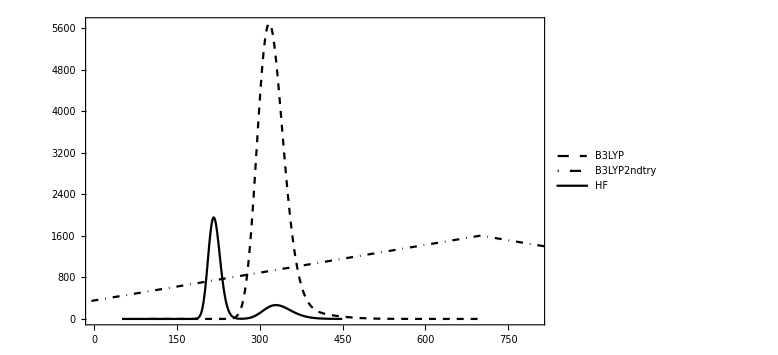

```mathematica
ListLinePlot[{#1,#2}&@@@Cases[Import[#,"Table"],{_Real,_Real,_Real}]&/@{"aspirinexcitedoptfreq_uvvis.txt","aspirinexcitedoptfreq2ndtry_uvvis.txt","aspirinexcitedoptfreqhf_uvvis.txt"},PlotRange->{{0,800},All},Frame->True,PlotStyle->{{Black,Dashed},{Black,DotDashed},Black},ImageSize->Large,Axes->False,PlotLegends->{{"B3LYP","B3LYP2ndtry","HF"}}]
```

```mathematica
SetDirectory["/Users/Apple/Documents/scf"];
```

```mathematica
FileNames[]
```

{.DS_Store,PBS,PBSrelax,qe_test.o1297983,qe_test.o1297988,qe_test.o1297994,qe_test.o1310604,qe_test.o1345506,relax15.in,relax15.out,relax8.in,relax8.out,sample.txt,scf10.in,scf10.out,scf11.in,scf11.out,scf12.in,scf12.out,scf13.in,scf13.out,scf14.in,scf14.out,scf15.in,scf15.out,scf16.in,scf16.out,scf17.in,scf17.out,scf18.in,scf18.out,scf19.in,scf19.out,scf20.in,scf20.out,scf21.in,scf21.out,scf22.in,scf22.out,scf23.in,scf23.out,scf24.in,scf24.out,scf25.in,scf25.out,scf4.in,scf4.out,scf5.in,scf5.out,scf6.in,scf6.out,scf7.in,scf7.out,scf8.in,scf8.out,scf9.in,scf9.out,scf.in,Walter-Feng.o1345089,Walter-Feng.o1366701,Walter-Feng.o1368705,Walter-Feng.o1368986}

```mathematica
Table[A[i]=Import[FileNames["*.out"][[i]]],{i,1,Length[FileNames["*.out"]]}];
```

```mathematica
FileNames["*.out"]
```

{relax15.out,relax8.out,scf10.out,scf11.out,scf12.out,scf13.out,scf14.out,scf15.out,scf16.out,scf17.out,scf18.out,scf19.out,scf20.out,scf21.out,scf22.out,scf23.out,scf24.out,scf25.out,scf4.out,scf5.out,scf6.out,scf7.out,scf8.out,scf9.out}

```mathematica
Cases[Flatten[ImportString[#,"Table"]&/@Take[ImportString[A[1],"Data"],#]&/@Position[StringCount[#,"total energy"]&/@ImportString[A[1],"Data"],1]],_Real]
```

{-382.246,-382.142,-382.676,-382.754,-382.584,-382.534,-382.558,-382.563,-382.564,-382.566,-382.557,-382.547,-382.548,-382.55,-382.549,-382.55,-382.55,-382.55,-382.549,-382.55,-382.549,-382.549,-382.549,-382.549,-382.549,-382.549}

```mathematica
FileNames["*.out"]
```

{relax15.out,relax8.out,scf10.out,scf11.out,scf12.out,scf13.out,scf14.out,scf15.out,scf16.out,scf17.out,scf18.out,scf19.out,scf20.out,scf21.out,scf22.out,scf23.out,scf24.out,scf25.out,scf4.out,scf5.out,scf6.out,scf7.out,scf8.out,scf9.out}

```mathematica
Delete[FileNames["*.out"],Position[totalenergylist,{}]]
```

{scf10.out,scf11.out,scf12.out,scf13.out,scf14.out,scf15.out,scf16.out,scf17.out,scf18.out,scf4.out,scf5.out,scf6.out,scf7.out,scf8.out,scf9.out}

```mathematica
Export["kpoint.eps",ListLinePlot[Transpose[{Table[i,{i,4,18}],Join[Take[Last/@Select[totalenergylist,Length[#]>0&],-6],Take[Last/@Select[totalenergylist,Length[#]>0&],9]]}],PlotRange->All,Frame->True,FrameLabel->{"k-point","Energy/Ry"}]]
```

kpoint.eps

```mathematica
totalenergylist=Table[Cases[Flatten[ImportString[#,"Table"]&/@Take[ImportString[A[i],"Data"],#]&/@Position[StringCount[#,"total energy"]&/@ImportString[A[i],"Data"],1]],_Real],{i,1,Length[FileNames["*.out"]]}];
```

ImportString::string: First argument {{},{Program PWSCF v.6.1 (svn rev. 13369) starts on 22Apr2018 at  8:23:46},{},{This program is part of the open-source Quantum ESPRESSO suite},«43»,{number of iterations used =            8  plain     mixing},{Exchange-correlation      = PBE ( 1  4  3  4 0 0)},{},«1245»} is not a string.

StringCount::strse: String or list of strings expected at position 1 in StringCount[{{},{Program PWSCF v.6.1 (svn rev. 13369) starts on 22Apr2018 at  8:23:46},{},{This program is part of the open-source Quantum ESPRESSO suite},«43»,{number of iterations used =            8  plain     mixing},{Exchange-correlation      = PBE ( 1  4  3  4 0 0)},{},«1245»},total energy].

ImportString::string: First argument StringCount[{{},{Program PWSCF v.6.1 (svn rev. 13369) starts on 22Apr2018 at  8:23:46},{},{This program is part of the open-source Quantum ESPRESSO suite},«43»,{number of iterations used =            8  plain     mixing},{Exchange-correlation      = PBE ( 1  4  3  4 0 0)},{},«1245»},total energy] is not a string.

ImportString::string: First argument {{},{Program PWSCF v.6.1 (svn rev. 13369) starts on 22Apr2018 at 13:23:46},{},{This program is part of the open-source Quantum ESPRESSO suite},«43»,{number of iterations used =            8  plain     mixing},{Exchange-correlation      = PBE ( 1  4  3  4 0 0)},{},«1039»} is not a string.

General::stop: Further output of ImportString::string will be suppressed during this calculation.

StringCount::strse: String or list of strings expected at position 1 in StringCount[{{},{Program PWSCF v.6.1 (svn rev. 13369) starts on 22Apr2018 at 13:23:46},{},{This program is part of the open-source Quantum ESPRESSO suite},«43»,{number of iterations used =            8  plain     mixing},{Exchange-correlation      = PBE ( 1  4  3  4 0 0)},{},«1039»},total energy].

StringCount::strse: String or list of strings expected at position 1 in StringCount[{{},{Program PWSCF v.6.1 (svn rev. 13369) starts on 22Apr2018 at 22:21:26},{},{This program is part of the open-source Quantum ESPRESSO suite},«43»,{number of iterations used =            8  plain     mixing},{Exchange-correlation      = PBE ( 1  4  3  4 0 0)},{},«1285»},total energy].

General::stop: Further output of StringCount::strse will be suppressed during this calculation.

```mathematica
Export["energyrecursion.eps",ListLinePlot[Select[totalenergylist,Length[#]>0&],PlotRange->All,Frame->True,FrameLabel->{"iteration","Energy/Ry"}]]
```

energyrecursion.eps

```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/Quantum Esppresso"];
```

```mathematica
FileNames[]
```

{ecut15.out,ecut20.out,ecut25.out,ecut30.out,ecut35.out,ecut40.out,ecut45.out,ecut50.out,ecut55.out,ecut60.out,graphene.xyz,neb.in,neb.out,PW1.out,PW2.out,PW3.out,PW4.out,PW5.out,PW6.out,PW7.out}

```mathematica
FileNames["ecut*.out"]
```

{ecut15.out,ecut20.out,ecut25.out,ecut30.out,ecut35.out,ecut40.out,ecut45.out,ecut50.out,ecut55.out,ecut60.out}

```mathematica
Table[ecut[i]=Import[FileNames["ecut*.out"][[i]]],{i,1,Length[FileNames["ecut*.out"]]}];
```

```mathematica
ecutenergylist=Table[Cases[Flatten[ImportString[#,"Table"]&/@Take[ImportString[ecut[i],"Data"],#]&/@Position[StringCount[#,"total energy"]&/@ImportString[ecut[i],"Data"],1]],_Real],{i,1,Length[FileNames["ecut*.out"]]}];
```

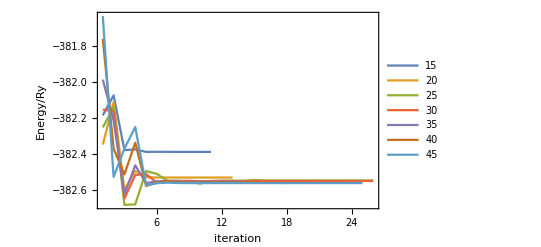

```mathematica
ListLinePlot[Drop[ecutenergylist,3],PlotRange->All,Frame->True,PlotLegends->Table[i,{i,15,60,5}],FrameLabel->{"iteration","Energy/Ry"}]
```

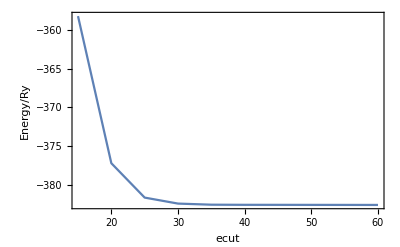

```mathematica
ListLinePlot[Transpose[{Table[i,{i,15,60,5}],Last/@ecutenergylist}],PlotRange->All,Frame->True,FrameLabel->{"ecut","Energy/Ry"}]
```

```mathematica
xyz=Import["graphene.xyz","Table"];
```

```mathematica
xyzreformed=Partition[DeleteCases[DeleteCases[xyz,{}],{36}],36];
```

```mathematica
PointCurveList=Interpolation[#][t]&/@Drop[Transpose[#],1]&/@Transpose[xyzreformed];
```

```mathematica
Frames=Table[Graphics3D[Join[Flatten@({Gray,Ball[#,0.8]}&/@Take[PointCurveList,32])/.t->a,Flatten@({Orange,Ball[#,1.2]}&/@Take[PointCurveList,{33,33}])/.t->a,Flatten@({Red,Ball[#,0.5]}&/@Take[PointCurveList,{34,34}])/.t->a,Flatten@({Blue,Ball[#,0.3]}&/@Take[PointCurveList,-2])/.t->a]],{a,1,7,0.001}];
```

```mathematica
ListAnimate[Frames,60]
```

```mathematica
Animate[Graphics3D[Join[Flatten@({Gray,Ball[#,0.8]}&/@Take[PointCurveList,32])/.t->a,Flatten@({Orange,Ball[#,1.2]}&/@Take[PointCurveList,{33,33}])/.t->a,Flatten@({Red,Ball[#,0.5]}&/@Take[PointCurveList,{34,34}])/.t->a,Flatten@({Blue,Ball[#,0.3]}&/@Take[PointCurveList,-2])/.t->a]],{a,1,7,0.1}]
```

```mathematica
{#1,#2}&@@@Cases[Import[#,"Table"],{_Real,_Real,_Real}]&/@{"aspirinexcitedoptfreq_uvvis.txt","aspirinexcitedoptfreq2ndtry_uvvis.txt","aspirinexcitedoptfreqhf_uvvis.txt"}
```

{{{100.,0.},{101.2,0.},{102.4,0.},{103.6,0.},{104.8,0.},{106.,0.},{107.2,0.},{108.4,0.},{109.6,0.},{110.8,0.},{112.,0.},{113.2,0.},{114.4,0.},{115.6,0.},{116.8,0.},{118.,0.},{119.2,0.},{120.4,0.},{121.6,0.},{122.8,0.},{124.,0.},{125.2,0.},{126.4,0.},{127.6,0.},{128.8,0.},{130.,0.},{131.2,0.},{132.4,0.},{133.6,0.},{134.8,0.},{136.,0.},{137.2,0.},{138.4,0.},{139.6,0.},{140.8,0.},{142.,0.},{143.2,0.},{144.4,0.},{145.6,0.},{146.8,0.},{148.,0.},{149.2,0.},{150.4,0.},{151.6,0.},{152.8,0.},{154.,0.},{155.2,0.},{156.4,0.},{157.6,0.},{158.8,0.},{160.,0.},{161.2,0.},{162.4,0.},{163.6,0.},{164.8,0.},{166.,0.},{167.2,0.},{168.4,0.},{169.6,0.},{170.8,0.},{172.,0.},{173.2,0.},{174.4,0.},{175.6,0.},{176.8,0.},{178.,0.},{179.2,0.},{180.4,0.},{181.6,0.},{182.8,0.},{184.,0.},{185.2,0.},{186.4,0.},{187.6,0.},{188.8,0.},{190.,0.},{191.2,0.},{192.4,0.},{193.6,0.},{194.8,0.},{196.,0.},{197.2,1.×10^-10},{198.4,3.×10^-10},{199.6,8.×10^-10},{200.8,2.2×10^-9},{202.,5.5×10^-9},{203.2,1.36×10^-8},{204.4,3.25×10^-8},{205.6,7.56×10^-8},{206.8,1.719×10^-7},{208.,3.812×10^-7},{209.2,8.259×10^-7},{210.4,1.7494×10^-6},{211.6,3.6249×10^-6},{212.8,7.3525×10^-6},{214.,0.0000146076},{215.2,0.0000284443},{216.4,0.0000543177},{217.6,0.000101782},{218.8,0.000187252},{220.,0.000338415},{221.2,0.000601131},{222.4,0.00105005},{223.6,0.00180465},{224.8,0.00305302},{226.,0.00508655},{227.2,0.00834978},{228.4,0.0135107},{229.6,0.0215586},{230.8,0.0339375},{232.,0.0527271},{233.2,0.0808819},{234.4,0.122545},{235.6,0.183451},{236.8,0.271442},{238.,0.397113},{239.2,0.574605},{240.4,0.822576},{241.6,1.16537},{242.8,1.63438},{244.,2.26968},{245.2,3.12182},{246.4,4.25397},{247.6,5.74414},{248.8,7.68775},{250.,10.2002},{251.2,13.4199},{252.4,17.5107},{253.6,22.665},{254.8,29.1061},{256.,37.0907},{257.2,46.9109},{258.4,58.895},{259.6,73.4088},{260.8,90.855},{262.,111.672},{263.2,136.331},{264.4,165.333},{265.6,199.203},{266.8,238.486},{268.,283.735},{269.2,335.506},{270.4,394.345},{271.6,460.779},{272.8,535.302},{274.,618.363},{275.2,710.353},{276.4,811.592},{277.6,922.317},{278.8,1042.67},{280.,1172.69},{281.2,1312.29},{282.4,1461.27},{283.6,1619.31},{284.8,1785.94},{286.,1960.56},{287.2,2142.47},{288.4,2330.81},{289.6,2524.62},{290.8,2722.83},{292.,2924.27},{293.2,3127.68},{294.4,3331.76},{295.6,3535.13},{296.8,3736.39},{298.,3934.14},{299.2,4126.97},{300.4,4313.5},{301.6,4492.4},{302.8,4662.39},{304.,4822.27},{305.2,4970.95},{306.4,5107.42},{307.6,5230.79},{308.8,5340.33},{310.,5435.38},{311.2,5515.48},{312.4,5580.27},{313.6,5629.53},{314.8,5663.2},{316.,5681.33},{317.2,5684.11},{318.4,5671.85},{319.6,5644.97},{320.8,5603.99},{322.,5549.53},{323.2,5482.28},{324.4,5403.02},{325.6,5312.57},{326.8,5211.8},{328.,5101.61},{329.2,4982.95},{330.4,4856.75},{331.6,4723.96},{332.8,4585.52},{334.,4442.36},{335.2,4295.39},{336.4,4145.47},{337.6,3993.45},{338.8,3840.13},{340.,3686.26},{341.2,3532.55},{342.4,3379.64},{343.6,3228.16},{344.8,3078.64},{346.,2931.59},{347.2,2787.44},{348.4,2646.59},{349.6,2509.38},{350.8,2376.1},{352.,2247.},{353.2,2122.27},{354.4,2002.06},{355.6,1886.51},{356.8,1775.67},{358.,1669.61},{359.2,1568.33},{360.4,1471.82},{361.6,1380.04},{362.8,1292.93},{364.,1210.41},{365.2,1132.37},{366.4,1058.7},{367.6,989.278},{368.8,923.964},{370.,862.614},{371.2,805.075},{372.4,751.189},{373.6,700.799},{374.8,653.742},{376.,609.855},{377.2,568.979},{378.4,530.952},{379.6,495.617},{380.8,462.821},{382.,432.413},{383.2,404.248},{384.4,378.183},{385.6,354.083},{386.8,331.818},{388.,311.262},{389.2,292.296},{390.4,274.806},{391.6,258.685},{392.8,243.831},{394.,230.146},{395.2,217.541},{396.4,205.93},{397.6,195.233},{398.8,185.376},{400.,176.288},{401.2,167.904},{402.4,160.164},{403.6,153.012},{404.8,146.395},{406.,140.267},{407.2,134.582},{408.4,129.299},{409.6,124.383},{410.8,119.797},{412.,115.511},{413.2,111.495},{414.4,107.725},{415.6,104.176},{416.8,100.827},{418.,97.6573},{419.2,94.6504},{420.4,91.7902},{421.6,89.0623},{422.8,86.454},{424.,83.9537},{425.2,81.5513},{426.4,79.2377},{427.6,77.0047},{428.8,74.8453},{430.,72.7531},{431.2,70.7225},{432.4,68.7488},{433.6,66.8276},{434.8,64.9554},{436.,63.1288},{437.2,61.3451},{438.4,59.602},{439.6,57.8974},{440.8,56.2296},{442.,54.5972},{443.2,52.9989},{444.4,51.4337},{445.6,49.9007},{446.8,48.3992},{448.,46.9287},{449.2,45.4887},{450.4,44.0787},{451.6,42.6984},{452.8,41.3476},{454.,40.026},{455.2,38.7335},{456.4,37.4699},{457.6,36.2349},{458.8,35.0286},{460.,33.8506},{461.2,32.701},{462.4,31.5794},{463.6,30.4858},{464.8,29.4199},{466.,28.3816},{467.2,27.3707},{468.4,26.3868},{469.6,25.4299},{470.8,24.4995},{472.,23.5954},{473.2,22.7174},{474.4,21.865},{475.6,21.0379},{476.8,20.2357},{478.,19.4582},{479.2,18.7048},{480.4,17.9752},{481.6,17.269},{482.8,16.5856},{484.,15.9247},{485.2,15.2859},{486.4,14.6685},{487.6,14.0723},{488.8,13.4966},{490.,12.9411},{491.2,12.4052},{492.4,11.8885},{493.6,11.3904},{494.8,10.9105},{496.,10.4483},{497.2,10.0032},{498.4,9.57493},{499.6,9.16287},{500.8,8.76656},{502.,8.38555},{503.2,8.01935},{504.4,7.66753},{505.6,7.32961},{506.8,7.00516},{508.,6.69373},{509.2,6.3949},{510.4,6.10823},{511.6,5.83332},{512.8,5.56976},{514.,5.31715},{515.2,5.07511},{516.4,4.84324},{517.6,4.62119},{518.8,4.4086},{520.,4.2051},{521.2,4.01037},{522.4,3.82406},{523.6,3.64586},{524.8,3.47546},{526.,3.31254},{527.2,3.15681},{528.4,3.00799},{529.6,2.86581},{530.8,2.72999},{532.,2.60027},{533.2,2.47641},{534.4,2.35816},{535.6,2.2453},{536.8,2.13759},{538.,2.03481},{539.2,1.93677},{540.4,1.84326},{541.6,1.75407},{542.8,1.66904},{544.,1.58797},{545.2,1.51069},{546.4,1.43705},{547.6,1.36686},{548.8,1.3},{550.,1.2363},{551.2,1.17562},{552.4,1.11783},{553.6,1.0628},{554.8,1.0104},{556.,0.960518},{557.2,0.913032},{558.4,0.867835},{559.6,0.824821},{560.8,0.783888},{562.,0.744942},{563.2,0.707888},{564.4,0.672638},{565.6,0.639109},{566.8,0.607219},{568.,0.576891},{569.2,0.54805},{570.4,0.520627},{571.6,0.494553},{572.8,0.469766},{574.,0.446202},{575.2,0.423803},{576.4,0.402513},{577.6,0.38228},{578.8,0.363051},{580.,0.344778},{581.2,0.327414},{582.4,0.310917},{583.6,0.295242},{584.8,0.28035},{586.,0.266203},{587.2,0.252765},{588.4,0.239999},{589.6,0.227874},{590.8,0.216358},{592.,0.20542},{593.2,0.195033},{594.4,0.185168},{595.6,0.1758},{596.8,0.166904},{598.,0.158457},{599.2,0.150436},{600.4,0.14282},{601.6,0.135589},{602.8,0.128724},{604.,0.122206},{605.2,0.116018},{606.4,0.110143},{607.6,0.104566},{608.8,0.0992712},{610.,0.094245},{611.2,0.0894737},{612.4,0.0849444},{613.6,0.080645},{614.8,0.0765638},{616.,0.0726898},{617.2,0.0690125},{618.4,0.0655219},{619.6,0.0622087},{620.8,0.0590638},{622.,0.0560786},{623.2,0.0532452},{624.4,0.0505557},{625.6,0.0480029},{626.8,0.0455799},{628.,0.04328},{629.2,0.0410969},{630.4,0.0390248},{631.6,0.0370579},{632.8,0.035191},{634.,0.0334189},{635.2,0.0317368},{636.4,0.0301402},{637.6,0.0286246},{638.8,0.0271859},{640.,0.0258203},{641.2,0.0245239},{642.4,0.0232933},{643.6,0.0221252},{644.8,0.0210162},{646.,0.0199635},{647.2,0.0189641},{648.4,0.0180153},{649.6,0.0171145},{650.8,0.0162594},{652.,0.0154475},{653.2,0.0146767},{654.4,0.0139448},{655.6,0.0132499},{656.8,0.0125901},{658.,0.0119637},{659.2,0.0113688},{660.4,0.0108039},{661.6,0.0102675},{662.8,0.00975816},{664.,0.00927444},{665.2,0.00881506},{666.4,0.00837878},{667.6,0.00796443},{668.8,0.0075709},{670.,0.00719713},{671.2,0.00684211},{672.4,0.00650489},{673.6,0.00618457},{674.8,0.0058803},{676.,0.00559124},{677.2,0.00531665},{678.4,0.00505577},{679.6,0.00480793},{680.8,0.00457245},{682.,0.00434871},{683.2,0.00413612},{684.4,0.00393412},{685.6,0.00374217},{686.8,0.00355976},{688.,0.00338641},{689.2,0.00322167},{690.4,0.00306509},{691.6,0.00291628},{692.8,0.00277483},{694.,0.00264039},{695.2,0.00251258},{696.4,0.00239109},{697.6,0.0022756},{698.8,0.0021658}},{{-200000.,1.34158},{-199100.,1.34155},{-198200.,1.34152},{-197300.,1.34149},{-196400.,1.34146},{-195500.,1.34142},{-194600.,1.34139},{-193700.,1.34136},{-192800.,1.34133},{-191900.,1.34129},{-191000.,1.34126},{-190100.,1.34123},{-189200.,1.34119},{-188300.,1.34116},{-187400.,1.34112},{-186500.,1.34109},{-185600.,1.34105},{-184700.,1.34102},{-183800.,1.34098},{-182900.,1.34094},{-182000.,1.34091},{-181100.,1.34087},{-180200.,1.34083},{-179300.,1.34079},{-178400.,1.34075},{-177500.,1.34071},{-176600.,1.34067},{-175700.,1.34063},{-174800.,1.34059},{-173900.,1.34055},{-173000.,1.34051},{-172100.,1.34047},{-171200.,1.34043},{-170300.,1.34038},{-169400.,1.34034},{-168500.,1.3403},{-167600.,1.34025},{-166700.,1.34021},{-165800.,1.34016},{-164900.,1.34012},{-164000.,1.34007},{-163100.,1.34003},{-162200.,1.33998},{-161300.,1.33993},{-160400.,1.33988},{-159500.,1.33983},{-158600.,1.33978},{-157700.,1.33973},{-156800.,1.33968},{-155900.,1.33963},{-155000.,1.33958},{-154100.,1.33953},{-153200.,1.33947},{-152300.,1.33942},{-151400.,1.33936},{-150500.,1.33931},{-149600.,1.33925},{-148700.,1.3392},{-147800.,1.33914},{-146900.,1.33908},{-146000.,1.33902},{-145100.,1.33896},{-144200.,1.3389},{-143300.,1.33884},{-142400.,1.33878},{-141500.,1.33872},{-140600.,1.33865},{-139700.,1.33859},{-138800.,1.33852},{-137900.,1.33845},{-137000.,1.33839},{-136100.,1.33832},{-135200.,1.33825},{-134300.,1.33818},{-133400.,1.33811},{-132500.,1.33803},{-131600.,1.33796},{-130700.,1.33789},{-129800.,1.33781},{-128900.,1.33773},{-128000.,1.33766},{-127100.,1.33758},{-126200.,1.3375},{-125300.,1.33742},{-124400.,1.33733},{-123500.,1.33725},{-122600.,1.33716},{-121700.,1.33708},{-120800.,1.33699},{-119900.,1.3369},{-119000.,1.33681},{-118100.,1.33671},{-117200.,1.33662},{-116300.,1.33653},{-115400.,1.33643},{-114500.,1.33633},{-113600.,1.33623},{-112700.,1.33613},{-111800.,1.33602},{-110900.,1.33592},{-110000.,1.33581},{-109100.,1.3357},{-108200.,1.33559},{-107300.,1.33547},{-106400.,1.33536},{-105500.,1.33524},{-104600.,1.33512},{-103700.,1.335},{-102800.,1.33487},{-101900.,1.33475},{-101000.,1.33462},{-100100.,1.33449},{-99200.,1.33435},{-98300.,1.33421},{-97400.,1.33407},{-96500.,1.33393},{-95600.,1.33379},{-94700.,1.33364},{-93800.,1.33349},{-92900.,1.33333},{-92000.,1.33317},{-91100.,1.33301},{-90200.,1.33285},{-89300.,1.33268},{-88400.,1.33251},{-87500.,1.33233},{-86600.,1.33215},{-85700.,1.33196},{-84800.,1.33178},{-83900.,1.33158},{-83000.,1.33138},{-82100.,1.33118},{-81200.,1.33097},{-80300.,1.33076},{-79400.,1.33054},{-78500.,1.33032},{-77600.,1.33009},{-76700.,1.32986},{-75800.,1.32962},{-74900.,1.32937},{-74000.,1.32912},{-73100.,1.32885},{-72200.,1.32859},{-71300.,1.32831},{-70400.,1.32803},{-69500.,1.32774},{-68600.,1.32744},{-67700.,1.32713},{-66800.,1.32681},{-65900.,1.32648},{-65000.,1.32614},{-64100.,1.32579},{-63200.,1.32544},{-62300.,1.32506},{-61400.,1.32468},{-60500.,1.32429},{-59600.,1.32388},{-58700.,1.32345},{-57800.,1.32301},{-56900.,1.32256},{-56000.,1.32209},{-55100.,1.3216},{-54200.,1.3211},{-53300.,1.32057},{-52400.,1.32003},{-51500.,1.31946},{-50600.,1.31887},{-49700.,1.31825},{-48800.,1.31761},{-47900.,1.31695},{-47000.,1.31625},{-46100.,1.31552},{-45200.,1.31476},{-44300.,1.31396},{-43400.,1.31313},{-42500.,1.31226},{-41600.,1.31134},{-40700.,1.31037},{-39800.,1.30935},{-38900.,1.30828},{-38000.,1.30715},{-37100.,1.30596},{-36200.,1.3047},{-35300.,1.30336},{-34400.,1.30194},{-33500.,1.30043},{-32600.,1.29883},{-31700.,1.29711},{-30800.,1.29528},{-29900.,1.29332},{-29000.,1.29121},{-28100.,1.28894},{-27200.,1.28649},{-26300.,1.28385},{-25400.,1.28097},{-24500.,1.27785},{-23600.,1.27444},{-22700.,1.2707},{-21800.,1.26658},{-20900.,1.26204},{-20000.,1.257},{-19100.,1.25138},{-18200.,1.24508},{-17300.,1.23797},{-16400.,1.22991},{-15500.,1.22069},{-14600.,1.21008},{-13700.,1.19773},{-12800.,1.18325},{-11900.,1.16606},{-11000.,1.1454},{-10100.,1.12023},{-9200.,1.08905},{-8300.,1.04972},{-7400.,0.999069},{-6500.,0.932322},{-5600.,0.842176},{-4700.,0.717659},{-3800.,0.544167},{-2900.,0.313285},{-2000.,0.0770849},{-1100.,0.000208073},{-200.,0.},{700.,1603.86},{1600.,0.904904},{2500.,0.430158},{3400.,0.770384},{4300.,0.992938},{5200.,1.12759},{6100.,1.21057},{7000.,1.26345},{7900.,1.29825},{8800.,1.32181},{9700.,1.33813},{10600.,1.34964},{11500.,1.35786},{12400.,1.36381},{13300.,1.36812},{14200.,1.37125},{15100.,1.37353},{16000.,1.37515},{16900.,1.3763},{17800.,1.37708},{18700.,1.37758},{19600.,1.37787},{20500.,1.378},{21400.,1.378},{22300.,1.37789},{23200.,1.37772},{24100.,1.37748},{25000.,1.3772},{25900.,1.37689},{26800.,1.37655},{27700.,1.3762},{28600.,1.37583},{29500.,1.37545},{30400.,1.37507},{31300.,1.37469},{32200.,1.3743},{33100.,1.37392},{34000.,1.37354},{34900.,1.37316},{35800.,1.37279},{36700.,1.37243},{37600.,1.37207},{38500.,1.37171},{39400.,1.37137},{40300.,1.37103},{41200.,1.3707},{42100.,1.37037},{43000.,1.37005},{43900.,1.36974},{44800.,1.36944},{45700.,1.36914},{46600.,1.36885},{47500.,1.36857},{48400.,1.36829},{49300.,1.36802},{50200.,1.36775},{51100.,1.36749},{52000.,1.36724},{52900.,1.367},{53800.,1.36675},{54700.,1.36652},{55600.,1.36629},{56500.,1.36606},{57400.,1.36584},{58300.,1.36563},{59200.,1.36542},{60100.,1.36521},{61000.,1.36501},{61900.,1.36481},{62800.,1.36462},{63700.,1.36443},{64600.,1.36424},{65500.,1.36406},{66400.,1.36389},{67300.,1.36371},{68200.,1.36354},{69100.,1.36338},{70000.,1.36321},{70900.,1.36305},{71800.,1.3629},{72700.,1.36274},{73600.,1.36259},{74500.,1.36245},{75400.,1.3623},{76300.,1.36216},{77200.,1.36202},{78100.,1.36189},{79000.,1.36175},{79900.,1.36162},{80800.,1.36149},{81700.,1.36136},{82600.,1.36124},{83500.,1.36112},{84400.,1.361},{85300.,1.36088},{86200.,1.36076},{87100.,1.36065},{88000.,1.36054},{88900.,1.36043},{89800.,1.36032},{90700.,1.36022},{91600.,1.36011},{92500.,1.36001},{93400.,1.35991},{94300.,1.35981},{95200.,1.35971},{96100.,1.35961},{97000.,1.35952},{97900.,1.35943},{98800.,1.35934},{99700.,1.35925},{100600.,1.35916},{101500.,1.35907},{102400.,1.35898},{103300.,1.3589},{104200.,1.35882},{105100.,1.35873},{106000.,1.35865},{106900.,1.35857},{107800.,1.3585},{108700.,1.35842},{109600.,1.35834},{110500.,1.35827},{111400.,1.35819},{112300.,1.35812},{113200.,1.35805},{114100.,1.35798},{115000.,1.35791},{115900.,1.35784},{116800.,1.35777},{117700.,1.3577},{118600.,1.35764},{119500.,1.35757},{120400.,1.35751},{121300.,1.35744},{122200.,1.35738},{123100.,1.35732},{124000.,1.35726},{124900.,1.3572},{125800.,1.35714},{126700.,1.35708},{127600.,1.35702},{128500.,1.35696},{129400.,1.35691},{130300.,1.35685},{131200.,1.3568},{132100.,1.35674},{133000.,1.35669},{133900.,1.35664},{134800.,1.35658},{135700.,1.35653},{136600.,1.35648},{137500.,1.35643},{138400.,1.35638},{139300.,1.35633},{140200.,1.35628},{141100.,1.35623},{142000.,1.35618},{142900.,1.35614},{143800.,1.35609},{144700.,1.35604},{145600.,1.356},{146500.,1.35595},{147400.,1.35591},{148300.,1.35587},{149200.,1.35582},{150100.,1.35578},{151000.,1.35574},{151900.,1.35569},{152800.,1.35565},{153700.,1.35561},{154600.,1.35557},{155500.,1.35553},{156400.,1.35549},{157300.,1.35545},{158200.,1.35541},{159100.,1.35537},{160000.,1.35534},{160900.,1.3553},{161800.,1.35526},{162700.,1.35522},{163600.,1.35519},{164500.,1.35515},{165400.,1.35511},{166300.,1.35508},{167200.,1.35504},{168100.,1.35501},{169000.,1.35497},{169900.,1.35494},{170800.,1.35491},{171700.,1.35487},{172600.,1.35484},{173500.,1.35481},{174400.,1.35477},{175300.,1.35474},{176200.,1.35471},{177100.,1.35468},{178000.,1.35465},{178900.,1.35462},{179800.,1.35458},{180700.,1.35455},{181600.,1.35452},{182500.,1.35449},{183400.,1.35446},{184300.,1.35443},{185200.,1.35441},{186100.,1.35438},{187000.,1.35435},{187900.,1.35432},{188800.,1.35429},{189700.,1.35426},{190600.,1.35424},{191500.,1.35421},{192400.,1.35418},{193300.,1.35416},{194200.,1.35413},{195100.,1.3541},{196000.,1.35408},{196900.,1.35405},{197800.,1.35402},{198700.,1.354},{199600.,1.35397},{200500.,1.35395},{201400.,1.35392},{202300.,1.3539},{203200.,1.35387},{204100.,1.35385},{205000.,1.35383},{205900.,1.3538},{206800.,1.35378},{207700.,1.35376},{208600.,1.35373},{209500.,1.35371},{210400.,1.35369},{211300.,1.35366},{212200.,1.35364},{213100.,1.35362},{214000.,1.3536},{214900.,1.35358},{215800.,1.35355},{216700.,1.35353},{217600.,1.35351},{218500.,1.35349},{219400.,1.35347},{220300.,1.35345},{221200.,1.35343},{222100.,1.35341},{223000.,1.35338},{223900.,1.35336},{224800.,1.35334},{225700.,1.35332},{226600.,1.3533},{227500.,1.35328},{228400.,1.35327},{229300.,1.35325},{230200.,1.35323},{231100.,1.35321},{232000.,1.35319},{232900.,1.35317},{233800.,1.35315},{234700.,1.35313},{235600.,1.35311},{236500.,1.3531},{237400.,1.35308},{238300.,1.35306},{239200.,1.35304},{240100.,1.35302},{241000.,1.35301},{241900.,1.35299},{242800.,1.35297},{243700.,1.35295},{244600.,1.35294},{245500.,1.35292},{246400.,1.3529},{247300.,1.35289},{248200.,1.35287},{249100.,1.35285}},{{50.,0.},{50.8,0.},{51.6,0.},{52.4,0.},{53.2,0.},{54.,0.},{54.8,0.},{55.6,0.},{56.4,0.},{57.2,0.},{58.,0.},{58.8,0.},{59.6,0.},{60.4,0.},{61.2,0.},{62.,0.},{62.8,0.},{63.6,0.},{64.4,0.},{65.2,0.},{66.,0.},{66.8,0.},{67.6,0.},{68.4,0.},{69.2,0.},{70.,0.},{70.8,0.},{71.6,0.},{72.4,0.},{73.2,0.},{74.,0.},{74.8,0.},{75.6,0.},{76.4,0.},{77.2,0.},{78.,0.},{78.8,0.},{79.6,0.},{80.4,0.},{81.2,0.},{82.,0.},{82.8,0.},{83.6,0.},{84.4,0.},{85.2,0.},{86.,0.},{86.8,0.},{87.6,0.},{88.4,0.},{89.2,0.},{90.,0.},{90.8,0.},{91.6,0.},{92.4,0.},{93.2,0.},{94.,0.},{94.8,0.},{95.6,0.},{96.4,0.},{97.2,0.},{98.,0.},{98.8,0.},{99.6,0.},{100.4,0.},{101.2,0.},{102.,0.},{102.8,0.},{103.6,0.},{104.4,0.},{105.2,0.},{106.,0.},{106.8,0.},{107.6,0.},{108.4,0.},{109.2,0.},{110.,0.},{110.8,0.},{111.6,0.},{112.4,0.},{113.2,0.},{114.,0.},{114.8,0.},{115.6,0.},{116.4,0.},{117.2,0.},{118.,0.},{118.8,0.},{119.6,0.},{120.4,0.},{121.2,0.},{122.,0.},{122.8,0.},{123.6,0.},{124.4,0.},{125.2,0.},{126.,0.},{126.8,0.},{127.6,0.},{128.4,0.},{129.2,0.},{130.,0.},{130.8,0.},{131.6,0.},{132.4,0.},{133.2,0.},{134.,0.},{134.8,0.},{135.6,0.},{136.4,0.},{137.2,0.},{138.,0.},{138.8,0.},{139.6,0.},{140.4,0.},{141.2,0.},{142.,0.},{142.8,0.},{143.6,0.},{144.4,0.},{145.2,0.},{146.,0.},{146.8,0.},{147.6,0.},{148.4,0.},{149.2,0.},{150.,0.},{150.8,0.},{151.6,0.},{152.4,0.},{153.2,0.},{154.,0.},{154.8,0.},{155.6,1.×10^-10},{156.4,2.×10^-10},{157.2,6.×10^-10},{158.,1.7×10^-9},{158.8,4.7×10^-9},{159.6,1.28×10^-8},{160.4,3.38×10^-8},{161.2,8.66×10^-8},{162.,2.163×10^-7},{162.8,5.257×10^-7},{163.6,1.2451×10^-6},{164.4,2.8753×10^-6},{165.2,6.4777×10^-6},{166.,0.0000142454},{166.8,0.0000305989},{167.6,0.0000642329},{168.4,0.000131846},{169.2,0.00026477},{170.,0.000520458},{170.8,0.00100194},{171.6,0.00188993},{172.4,0.00349471},{173.2,0.00633783},{174.,0.0112779},{174.8,0.0197004},{175.6,0.0337956},{176.4,0.0569601},{177.2,0.0943594},{178.,0.153701},{178.8,0.246273},{179.6,0.3883},{180.4,0.602686},{181.2,0.921182},{182.,1.38702},{182.8,2.05804},{183.6,3.01024},{184.4,4.3418},{185.2,6.17727},{186.,8.67196},{186.8,12.0161},{187.6,16.4385},{188.4,22.2096},{189.2,29.643},{190.,39.0952},{190.8,50.964},{191.6,65.6831},{192.4,83.7157},{193.2,105.543},{194.,131.653},{194.8,162.522},{195.6,198.597},{196.4,240.277},{197.2,287.891},{198.,341.674},{198.8,401.751},{199.6,468.116},{200.4,540.613},{201.2,618.934},{202.,702.6},{202.8,790.971},{203.6,883.246},{204.4,978.472},{205.2,1075.57},{206.,1173.34},{206.8,1270.51},{207.6,1365.76},{208.4,1457.73},{209.2,1545.11},{210.,1626.62},{210.8,1701.07},{211.6,1767.38},{212.4,1824.61},{213.2,1872.},{214.,1908.96},{214.8,1935.08},{215.6,1950.16},{216.4,1954.18},{217.2,1947.33},{218.,1929.94},{218.8,1902.54},{219.6,1865.76},{220.4,1820.38},{221.2,1767.26},{222.,1707.33},{222.8,1641.58},{223.6,1571.01},{224.4,1496.62},{225.2,1419.4},{226.,1340.29},{226.8,1260.2},{227.6,1179.95},{228.4,1100.31},{229.2,1021.95},{230.,945.462},{230.8,871.365},{231.6,800.079},{232.4,731.944},{233.2,667.223},{234.,606.103},{234.8,548.703},{235.6,495.083},{236.4,445.245},{237.2,399.147},{238.,356.707},{238.8,317.807},{239.6,282.306},{240.4,250.04},{241.2,220.832},{242.,194.493},{242.8,170.83},{243.6,149.647},{244.4,130.752},{245.2,113.952},{246.,99.0662},{246.8,85.9173},{247.6,74.339},{248.4,64.1745},{249.2,55.2775},{250.,47.5125},{250.8,40.7549},{251.6,34.8906},{252.4,29.816},{253.2,25.4372},{254.,21.67},{254.8,18.4389},{255.6,15.6766},{256.4,13.3238},{257.2,11.3278},{258.,9.64289},{258.8,8.22883},{259.6,7.05091},{260.4,6.07921},{261.2,5.28816},{262.,4.65607},{262.8,4.16474},{263.6,3.79908},{264.4,3.54679},{265.2,3.39804},{266.,3.34519},{266.8,3.38255},{267.6,3.50618},{268.4,3.71368},{269.2,4.004},{270.,4.37733},{270.8,4.83489},{271.6,5.37888},{272.4,6.01228},{273.2,6.73881},{274.,7.56281},{274.8,8.48911},{275.6,9.52301},{276.4,10.6701},{277.2,11.9363},{278.,13.3277},{278.8,14.8503},{279.6,16.5104},{280.4,18.3141},{281.2,20.2672},{282.,22.3757},{282.8,24.6449},{283.6,27.0799},{284.4,29.6853},{285.2,32.4652},{286.,35.4232},{286.8,38.5622},{287.6,41.8843},{288.4,45.391},{289.2,49.0828},{290.,52.9594},{290.8,57.0196},{291.6,61.2613},{292.4,65.6814},{293.2,70.2759},{294.,75.0395},{294.8,79.9662},{295.6,85.0489},{296.4,90.2795},{297.2,95.6488},{298.,101.147},{298.8,106.763},{299.6,112.485},{300.4,118.301},{301.2,124.197},{302.,130.159},{302.8,136.172},{303.6,142.222},{304.4,148.292},{305.2,154.367},{306.,160.43},{306.8,166.464},{307.6,172.454},{308.4,178.381},{309.2,184.23},{310.,189.984},{310.8,195.626},{311.6,201.142},{312.4,206.514},{313.2,211.728},{314.,216.77},{314.8,221.626},{315.6,226.282},{316.4,230.726},{317.2,234.946},{318.,238.932},{318.8,242.674},{319.6,246.163},{320.4,249.391},{321.2,252.351},{322.,255.036},{322.8,257.443},{323.6,259.567},{324.4,261.405},{325.2,262.956},{326.,264.218},{326.8,265.192},{327.6,265.878},{328.4,266.279},{329.2,266.398},{330.,266.237},{330.8,265.803},{331.6,265.099},{332.4,264.133},{333.2,262.91},{334.,261.439},{334.8,259.726},{335.6,257.781},{336.4,255.612},{337.2,253.229},{338.,250.641},{338.8,247.858},{339.6,244.892},{340.4,241.751},{341.2,238.447},{342.,234.99},{342.8,231.392},{343.6,227.662},{344.4,223.813},{345.2,219.854},{346.,215.797},{346.8,211.651},{347.6,207.428},{348.4,203.136},{349.2,198.787},{350.,194.39},{350.8,189.954},{351.6,185.489},{352.4,181.002},{353.2,176.503},{354.,172.},{354.8,167.501},{355.6,163.012},{356.4,158.541},{357.2,154.095},{358.,149.68},{358.8,145.301},{359.6,140.965},{360.4,136.676},{361.2,132.439},{362.,128.259},{362.8,124.14},{363.6,120.085},{364.4,116.099},{365.2,112.183},{366.,108.34},{366.8,104.574},{367.6,100.885},{368.4,97.2767},{369.2,93.7496},{370.,90.3051},{370.8,86.9442},{371.6,83.6678},{372.4,80.4764},{373.2,77.3701},{374.,74.3493},{374.8,71.4137},{375.6,68.5632},{376.4,65.7972},{377.2,63.1153},{378.,60.5166},{378.8,58.0004},{379.6,55.5656},{380.4,53.2111},{381.2,50.9358},{382.,48.7384},{382.8,46.6175},{383.6,44.5717},{384.4,42.5995},{385.2,40.6993},{386.,38.8696},{386.8,37.1086},{387.6,35.4148},{388.4,33.7865},{389.2,32.2218},{390.,30.7192},{390.8,29.2768},{391.6,27.893},{392.4,26.5659},{393.2,25.2939},{394.,24.0752},{394.8,22.9082},{395.6,21.7911},{396.4,20.7223},{397.2,19.7001},{398.,18.7229},{398.8,17.7891},{399.6,16.8971},{400.4,16.0454},{401.2,15.2325},{402.,14.457},{402.8,13.7173},{403.6,13.0121},{404.4,12.3401},{405.2,11.6998},{406.,11.09},{406.8,10.5095},{407.6,9.95699},{408.4,9.43133},{409.2,8.93138},{410.,8.45603},{410.8,8.0042},{411.6,7.57487},{412.4,7.16703},{413.2,6.77973},{414.,6.41203},{414.8,6.06305},{415.6,5.73192},{416.4,5.41781},{417.2,5.11993},{418.,4.83751},{418.8,4.56983},{419.6,4.31617},{420.4,4.07587},{421.2,3.84827},{422.,3.63275},{422.8,3.42872},{423.6,3.23562},{424.4,3.05289},{425.2,2.88003},{426.,2.71652},{426.8,2.56191},{427.6,2.41573},{428.4,2.27755},{429.2,2.14697},{430.,2.02359},{430.8,1.90703},{431.6,1.79694},{432.4,1.69298},{433.2,1.59482},{434.,1.50217},{434.8,1.41471},{435.6,1.33219},{436.4,1.25433},{437.2,1.18087},{438.,1.1116},{438.8,1.04626},{439.6,0.984662},{440.4,0.926587},{441.2,0.871845},{442.,0.820252},{442.8,0.771635},{443.6,0.725826},{444.4,0.682672},{445.2,0.642022},{446.,0.603737},{446.8,0.567684},{447.6,0.533737},{448.4,0.501777},{449.2,0.471691}}}

```mathematica
Table[("ecut"<>ToString[i]<>".txt")~Export~("&control\n    calculation = 'scf'\n    restart_mode='from_scratch',\n    pseudo_dir = '~/backup/reaction',\n    outdir = './',\n    prefix='graphite',\n    tstress = .false.\n    tprnfor = .true.\n    nstep = 1000\n /\n &system\n    ibrav=0 ,celldm(1)=18.6,\n    nat=32 , ntyp=1 ,\n    ecutwfc ="<>ToString[i]<>" ,\n    ecutrho ="<>ToString[10i]<>" ,\n    occupations='smearing',\n    degauss=0.01\n /\n &electrons\n    diagonalization='david'\n    mixing_mode = 'plain'\n    mixing_beta = 0.5D0\n    conv_thr =  1.0d-6\n /\nATOMIC_SPECIES\n  C    12.0110   C.pbe-n-rrkjus_psl.0.1.UPF\nATOMIC_POSITIONS {crystal}\nC  0 0 0.249999999999999 \nC  0.0833333333333335 0.166666666666666 0.249999999999999 \nC  0.25 0 0.249999999999999 \nC  0.333333333333333 0.166666666666667 0.249999999999999 \nC  0.5 0 0.249999999999999 \nC  0.583333333333333 0.166666666666667 0.249999999999999 \nC  0.75 0 0.249999999999999 \nC  0.833333333333333 0.166666666666667 0.249999999999999 \nC  0 0.25 0.249999999999999 \nC  0.0833333333333335 0.416666666666666 0.249999999999999 \nC  0.25 0.25 0.249999999999999 \nC  0.333333333333333 0.416666666666666 0.249999999999999 \nC  0.5 0.25 0.249999999999999 \nC  0.583333333333333 0.416666666666666 0.249999999999999 \nC  0.75 0.25 0.249999999999999 \nC  0.833333333333333 0.416666666666666 0.249999999999999 \nC  0 0.5 0.249999999999999 \nC  0.0833333333333335 0.666666666666666 0.249999999999999 \nC  0.25 0.5 0.249999999999999 \nC  0.333333333333333 0.666666666666666 0.249999999999999 \nC  0.5 0.5 0.249999999999999 \nC  0.583333333333333 0.666666666666666 0.249999999999999 \nC  0.75 0.5 0.249999999999999 \nC  0.833333333333333 0.666666666666667 0.249999999999999 \nC  0 0.75 0.249999999999999 \nC  0.0833333333333335 0.916666666666666 0.249999999999999 \nC  0.25 0.75 0.249999999999999 \nC  0.333333333333333 0.916666666666666 0.249999999999999 \nC  0.5 0.75 0.249999999999999 \nC  0.583333333333333 0.916666666666666 0.249999999999999 \nC  0.75 0.75 0.249999999999999 \nC  0.833333333333333 0.916666666666666 0.249999999999999 \n\nK_POINTS {automatic}\n14 14 1 0 0 0\n\nCELL_PARAMETERS\n1.00000  0.00000 0.00000\n-0.50000 0.86602 0.00000\n0.00000  0.00000 2.76422"),{i,10,60,5}];
```

```mathematica
StringJoin@@Table["mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut"<>ToString[i]<>".in >"<>"ecut"<>ToString[i]<>".out\n",{i,10,60,5}]
```

mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut10.in >ecut10.out
mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut15.in >ecut15.out
mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut20.in >ecut20.out
mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut25.in >ecut25.out
mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut30.in >ecut30.out
mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut35.in >ecut35.out
mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut40.in >ecut40.out
mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut45.in >ecut45.out
mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut50.in >ecut50.out
mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut55.in >ecut55.out
mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut60.in >ecut60.out

```mathematica
"mpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut10.in >ecut10.out\nmpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut15.in >ecut15.out\nmpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut20.in >ecut20.out\nmpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut25.in >ecut25.out\nmpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut30.in >ecut30.out\nmpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut35.in >ecut35.out\nmpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut40.in >ecut40.out\nmpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut45.in >ecut45.out\nmpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut50.in >ecut50.out\nmpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut55.in >ecut55.out\nmpirun -np $nprocs -machinefile $PBS_NODEFILE pw.x<ecut60.in >ecut60.out"
```